# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["C:\\Users\\Miguel\\Github\\Entropy\\Faster entropy calculation\\QMB_offline.wl"];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

# T1

```mathematica
L=8;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
g=1;
h=0.01;
H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
La=L/2;
Lb=L-La;
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
```

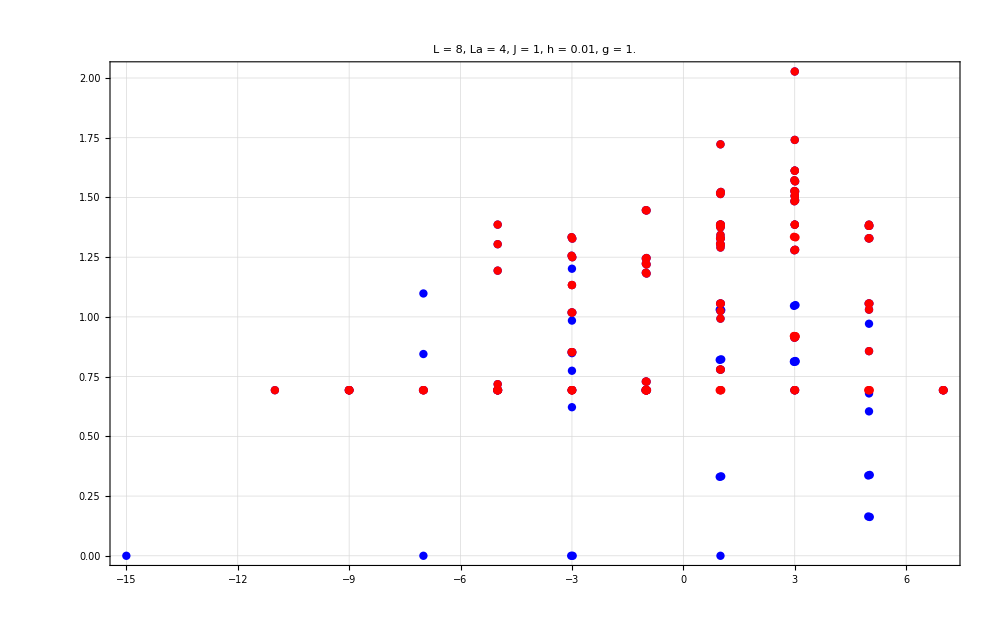

```mathematica
ListPlot[{Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Blue,PointSize[0.006]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]]
```

```mathematica
tlist=Table[i,{i,0,500,0.1}];
tlist//Length
```

5001

```mathematica
allstates=Table[RandomChainProductState[L],50];
probs=ParallelTable[Quiet[StandardDeviation[Abs[Conjugate[allvecs].i]^2]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{probs,allstates}],First];
productstatesfull=data[[All,2]];
```

```mathematica
svntproductfull=ParallelTable[{t,svn[L,La,Lb,j,allvals,allvecs,t]},{j,productstatesfull},{t,tlist},DistributedContexts->Full,Method->"CoarsestGrained"];
```

## Full RPS vs Positive parity, full RPS

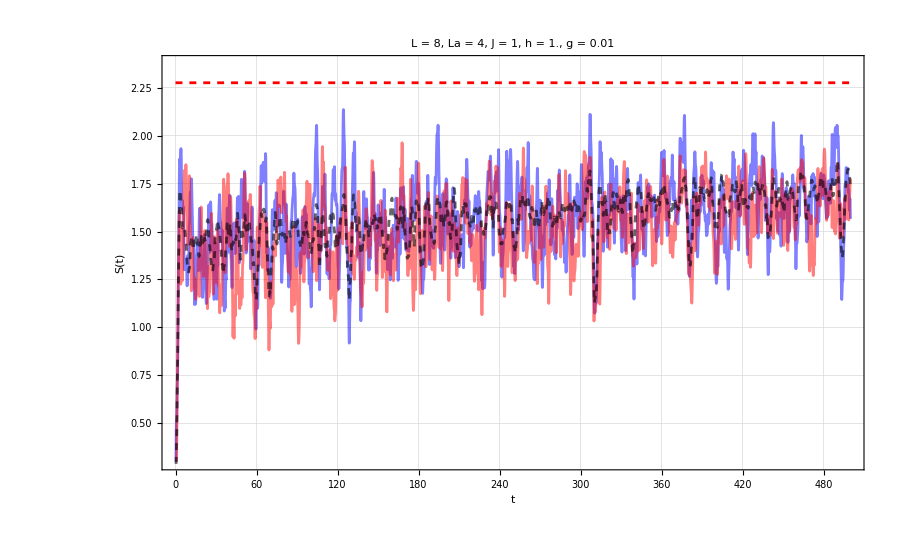

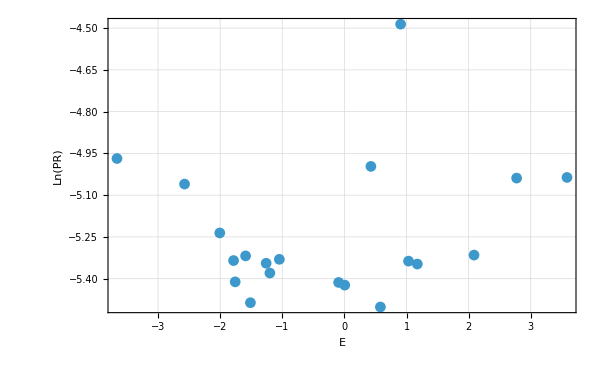

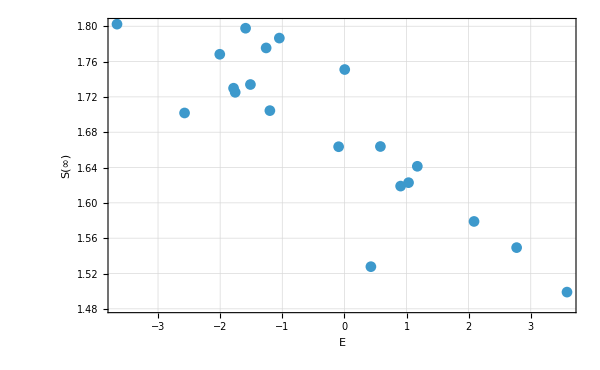

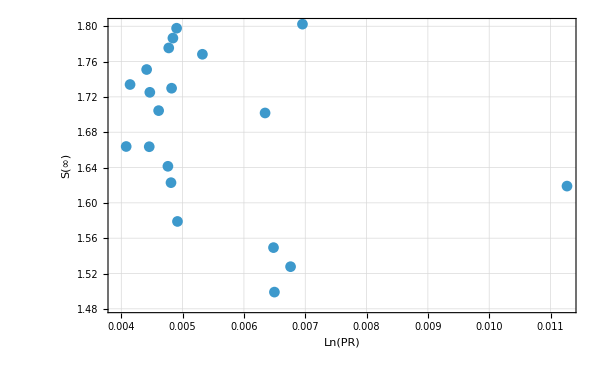

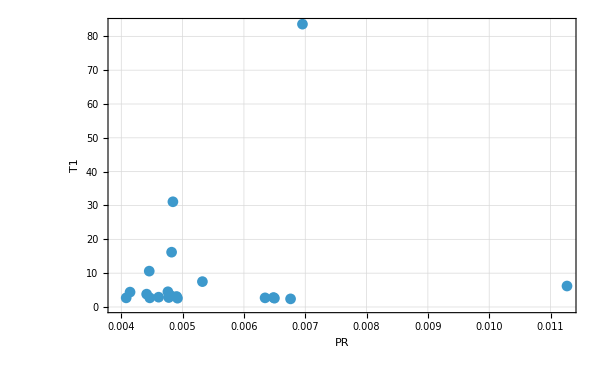

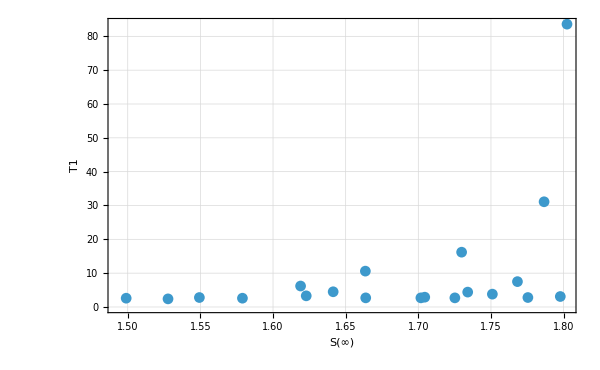

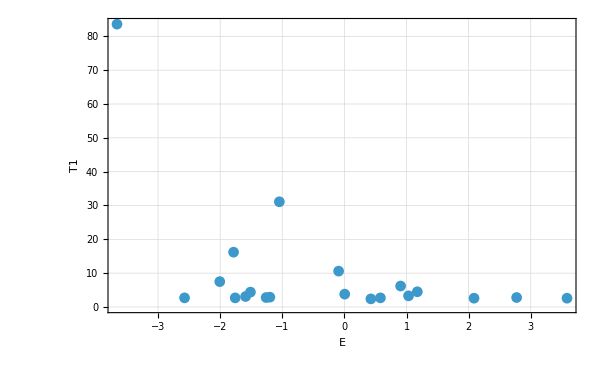

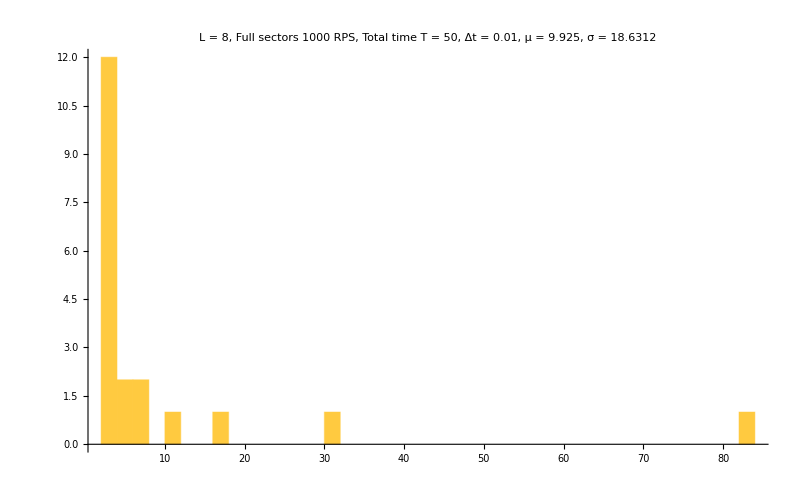

```mathematica
Show[{ListPlot[{svntproductfull[[1]],svntproductfull[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],ListPlot[Mean[svntproductfull],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproductfull[[j]];
times=tlist;
series=list[[All,2]];
limit=Mean[series[[-1000;;-1]]];
position=FirstPosition[series-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstatesfull]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstatesfull},DistributedContexts->Full];
infofull=Transpose[{sortediprs,t1s,limits,energies,productstatesfull}];
unsortedlimits=infofull[[All,3]];
ListPlot[Transpose[{infofull[[All,4]],Log[infofull[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["Ln(PR)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,4]],infofull[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["S(∞)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,1]],infofull[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["Ln(PR)",20,Black],Style["S(∞)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,1]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["PR",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,3]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["S(∞)",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,4]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
Histogram[infofull[[All,2]],50,PlotRange->All,ImageSize->800,PlotLabel->Style["L = 8, Full sectors 1000 RPS, Total time T = 50, Δt = 0.01, μ = "<>ToString[Mean[infofull[[All,2]]]]<>", σ = "<>ToString[StandardDeviation[infofull[[All,2]]]],20,Black]]
```

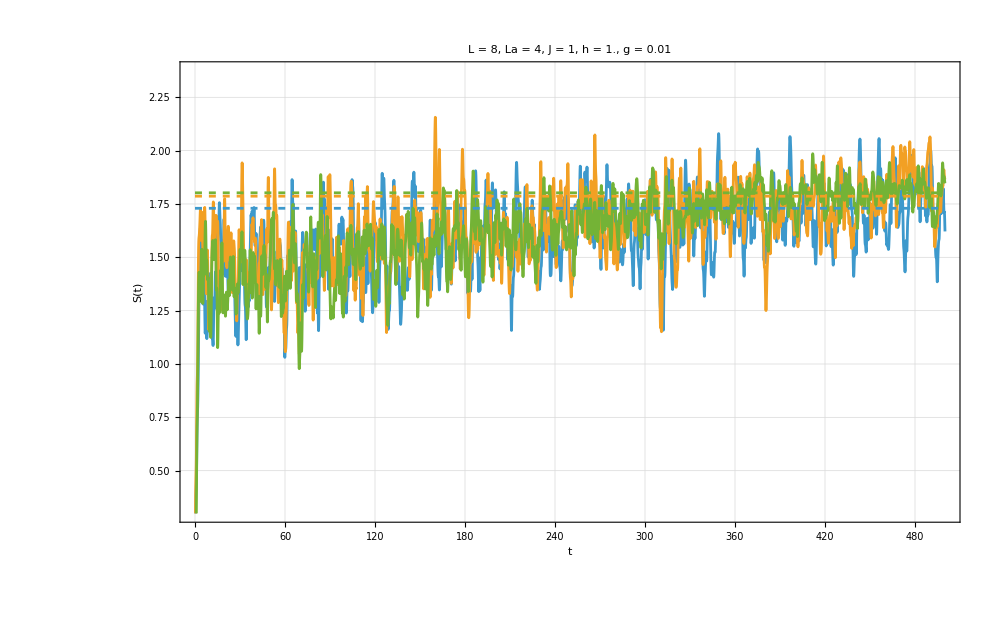

```mathematica
FAKEINFO=SortBy[Transpose[{t1s,sortediprs,limits,energies,productstatesfull,svntproductfull}],First];
fakelimits=FAKEINFO[[All,3]];
Show[{ListPlot[{FAKEINFO[[-3,6]],FAKEINFO[[-2,6]],FAKEINFO[[-1,6]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],Plot[{fakelimits[[-3]],fakelimits[[-2]],fakelimits[[-1]]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->Dashed]}]
```

# SVD

```mathematica
Clear[new];
new[ini_,t_,L_]:=Module[{schmidt,psit,ck=Conjugate[allvecs] . ini},
psit=ArrayReshape[N[Total[ ck * Exp[-I*allvals*t] * allvecs]],{2^(L/2),2^(L/2)}];
schmidt=Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]
];
```

```mathematica
allstates=Table[RandomChainProductState[L],20];
probs=ParallelTable[Quiet[StandardDeviation[Abs[Conjugate[allvecs].i]^2]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{probs,allstates}],First];
productstatesfull=data[[All,2]];
```

```mathematica
tlist=Table[i,{i,0,500,0.1}];
tlist//Length
```

5001

```mathematica
SetSharedVariable[allvals,allvecs,productstatesfull,tlist];
```

```mathematica
entropy2=ParallelTable[{t,new[j,t,L]},{j,productstatesfull},{t,tlist},DistributedContexts->None];
```

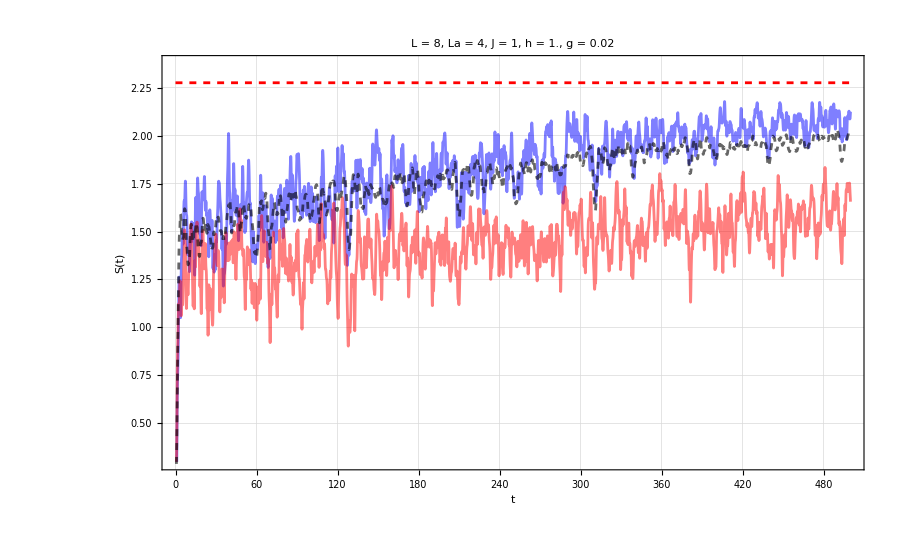

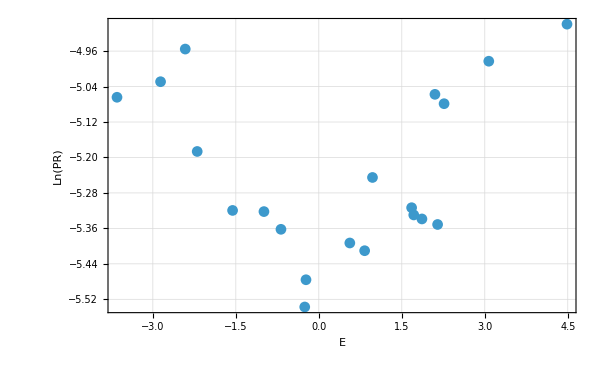

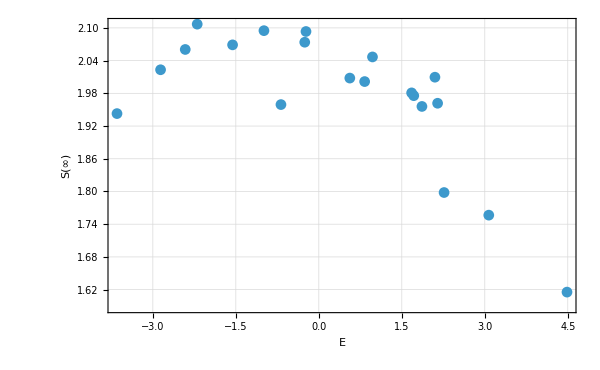

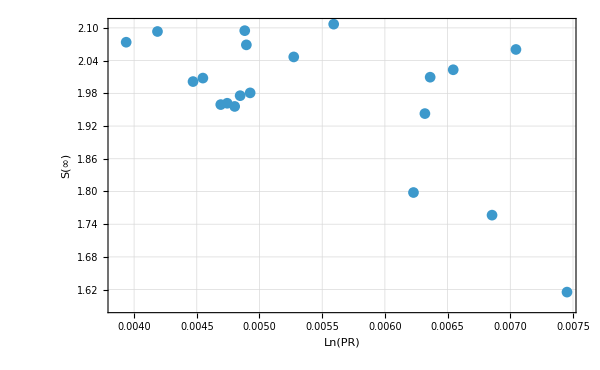

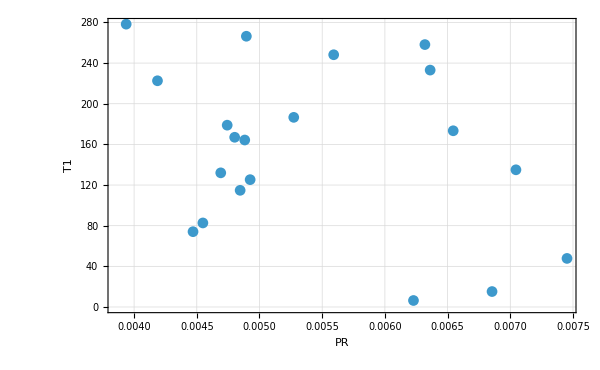

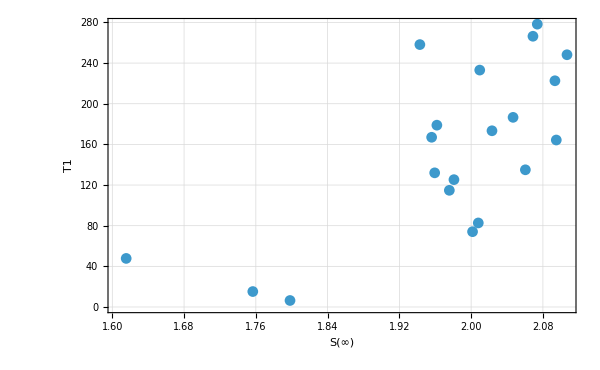

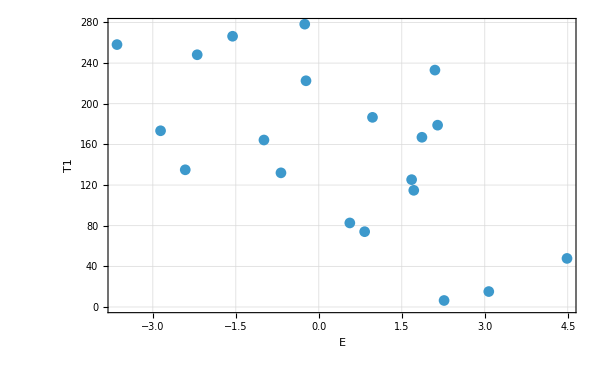

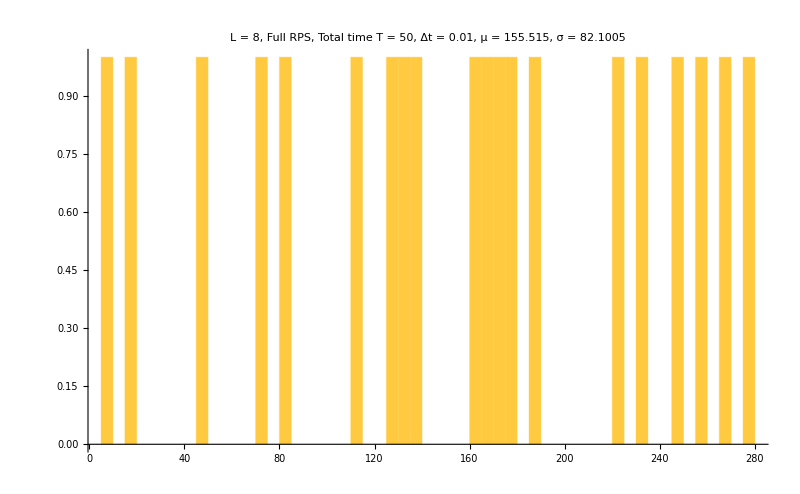

```mathematica
Show[{ListPlot[{entropy2[[1]],entropy2[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],ListPlot[Mean[entropy2],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=entropy2[[j]];
times=tlist;
series=list[[All,2]];
limit=Mean[series[[-200;;-1]]];
position=FirstPosition[series-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstatesfull]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstatesfull},DistributedContexts->Full];
infofull=Transpose[{sortediprs,t1s,limits,energies,productstatesfull}];
unsortedlimits=infofull[[All,3]];
ListPlot[Transpose[{infofull[[All,4]],Log[infofull[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["Ln(PR)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,4]],infofull[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["S(∞)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,1]],infofull[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["Ln(PR)",20,Black],Style["S(∞)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,1]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["PR",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,3]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["S(∞)",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,4]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
Histogram[infofull[[All,2]],50,PlotRange->All,ImageSize->800,PlotLabel->Style["L = 8, Full RPS, Total time T = 50, Δt = 0.01, μ = "<>ToString[Mean[infofull[[All,2]]]]<>", σ = "<>ToString[StandardDeviation[infofull[[All,2]]]],20,Black]]
```

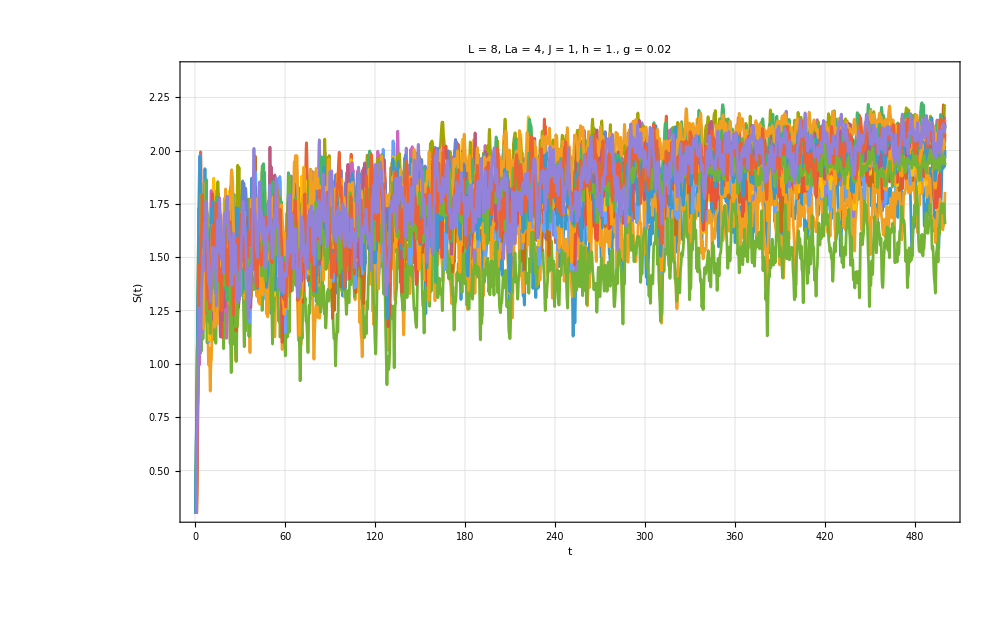

```mathematica
FAKEINFO=SortBy[Transpose[{t1s,sortediprs,limits,energies,productstatesfull,entropy2}],First];
ListPlot[FAKEINFO[[All,-1]],PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}]
```

```mathematica
states=FAKEINFO[[All,-2]];
```

```mathematica
FAKEINFO[[All,1]]
FAKEINFO[[All,2]]
```

{6.4,15.2,47.8,74.1,82.7,114.8,125.3,132.,135.,164.3,167.,173.4,178.9,186.6,222.6,233.1,248.2,258.2,266.4,278.3}

{0.00622794,0.00685444,0.00745221,0.00446999,0.00454854,0.0048457,0.00492543,0.00469107,0.00704505,0.00488241,0.00480213,0.00654484,0.00474248,0.00527319,0.00418653,0.00636098,0.00559169,0.00631902,0.00489531,0.00393695}

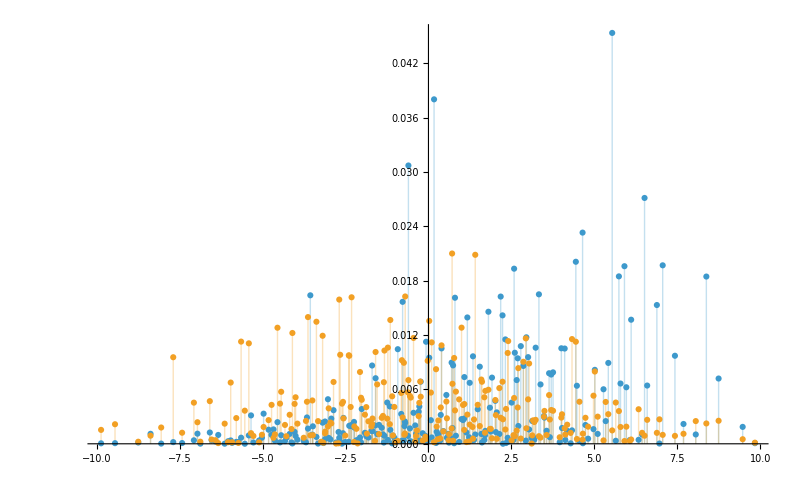

```mathematica
ListPlot[{Transpose[{allvals,Abs[Conjugate[allvecs].states[[1]]]^2}],Transpose[{allvals,Abs[Conjugate[allvecs].states[[-1]]]^2}]},PlotRange->All,Filling->Bottom,ImageSize->800]
```

```mathematica
probs=Table[Abs[Conjugate[allvecs].i]^2,{i,states}];
```

```mathematica
means=Table[i.allvals,{i,probs}];
```

```mathematica
probs//Dimensions
```

{20,256}

```mathematica
means//Dimensions
```

{20}

```mathematica
sigmas=Table[Sqrt[Total[probs[[i]]*(allvals-means[[i]])^2]],{i,Length[states]}]
```

{3.23265,2.67492,3.12227,3.63019,3.54854,3.13748,3.3068,3.08668,3.60142,3.43597,3.37763,3.56442,3.77591,3.39367,3.49683,3.03086,2.82272,3.37318,2.90137,3.26062}

# Single state

```mathematica
Clear[new];
new[ini_List,t_,L_Integer]:=Module[{schmidt,psit,ck=Conjugate[allvecs] . ini},
psit=ArrayReshape[N[Total[ ck * Exp[-I*allvals*t] * allvecs]],{2^(L/2),2^(L/2)}];
schmidt=Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]
];
```

```mathematica
L=8;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
g=1;
h=0.1;
H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
La=L/2;
Lb=L-La;
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
```

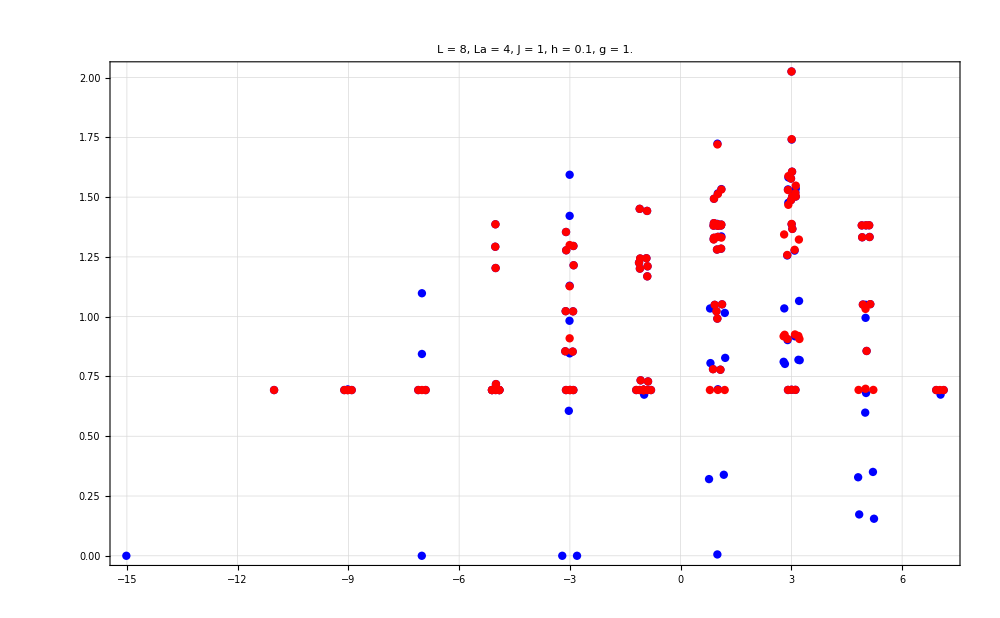

```mathematica
ListPlot[{Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Blue,PointSize[0.006]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]]
```

```mathematica
tlist=Table[i,{i,0,2000,0.1}];
tlist//Length
```

20001

```mathematica
tlist=Table[10^i,{i,0,4,0.0005}];
tlist//Length
```

8001

```mathematica
productstatesfull=Table[RandomChainProductState[L],{i,10}];
```

```mathematica
(*SetSharedVariable[allvals,allvecs,productstatesfull,tlist];*)
```

```mathematica
svntproductfull=ParallelTable[{t,new[j,t,L]},{j,productstatesfull},{t,tlist},DistributedContexts->Full,Method->"CoarsestGrained"];
```

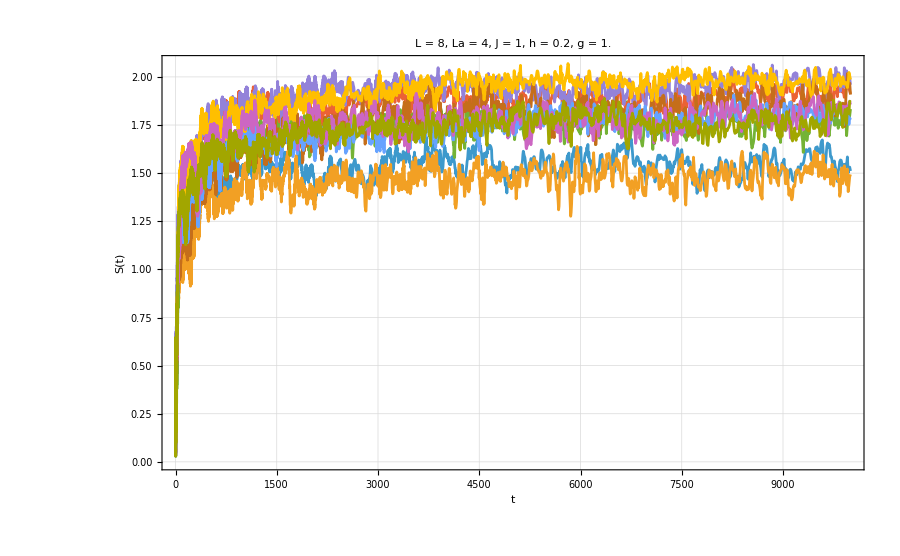

```mathematica
ListPlot[svntproductfull,PlotRange->All,Joined->True,ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}]
```

```mathematica
plots=Table[ListPlot[svntproductfull[[i]],PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->False,ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],{i,Length[productstatesfull]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[allvecs].i]^4],{i,productstatesfull}];
```

```mathematica
t1s={};
limits={};
Do[
list=svntproductfull[[j]];
times=tlist;
series=list[[All,2]];
limit=Mean[series[[-1000;;-1]]];
position=FirstPosition[series-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstatesfull]}];
```

```mathematica
info=SortBy[Transpose[{t1s,limits,1/iprs}],First];
```

```mathematica
info//TableForm
```

588.2 | 1.67891 | 65.3369
631.4 | 1.65655 | 67.6803
634.4 | 1.55538 | 43.3755
635.8 | 1.47696 | 59.9656
644.7 | 1.61164 | 88.6791
656.4 | 1.55765 | 49.6306
679.9 | 1.81725 | 110.326
705.3 | 1.41648 | 36.8619
707.7 | 1.593 | 54.2608
718.1 | 1.60236 | 29.2361

1.8765×10^14

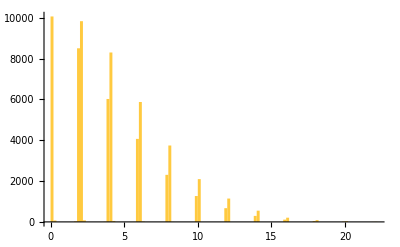

```mathematica
(*2. all pairwise absolute differences*)
allDiffs=Flatten[Abs[Outer[Subtract,Sort[allvals],Sort[allvals]]],1];
(*3. drop the zeros (i=j)*)
nonzeroDiffs=Select[allDiffs,#>0&];
(*4. smallest*)
minAll=Min[nonzeroDiffs];
1/minAll
Histogram[allDiffs,100]
```

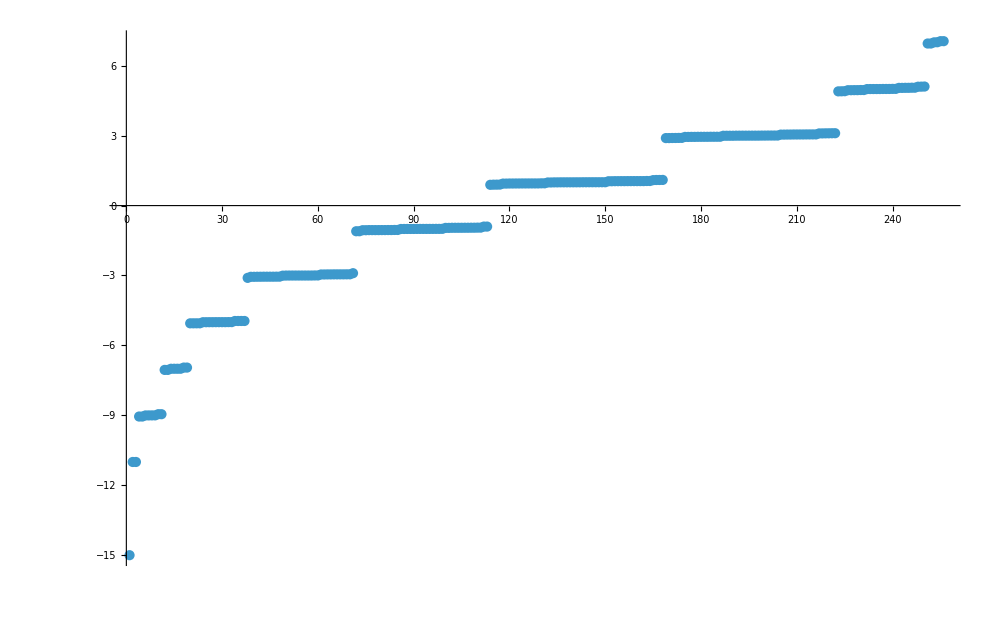

```mathematica
ListPlot[allvals,ImageSize->1000]
```

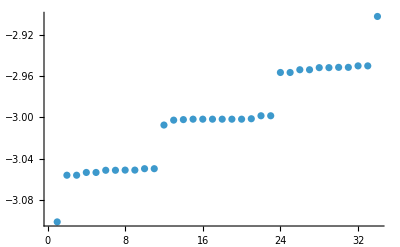

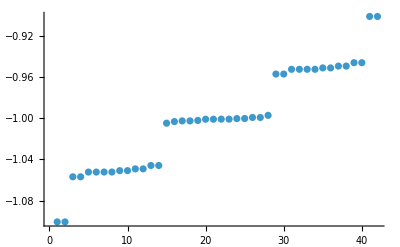

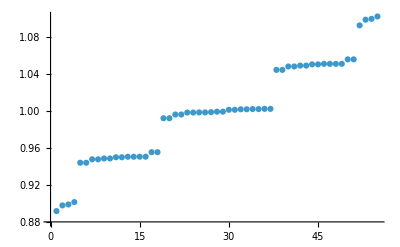

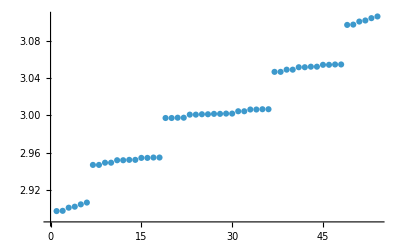

```mathematica
ListPlot[allvals[[38;;71]],PlotRange->All]
ListPlot[allvals[[72;;113]],PlotRange->All]
ListPlot[allvals[[114;;168]],PlotRange->All]
ListPlot[allvals[[169;;222]],PlotRange->All]
```

```mathematica
(*2. all pairwise absolute differences*)
allDiffs=Flatten[Abs[Outer[Subtract,allvals[[72;;113]],allvals[[72;;113]]]],1];
(*3. drop the zeros (i=j)*)
nonzeroDiffs=Select[allDiffs,#>0&];
```

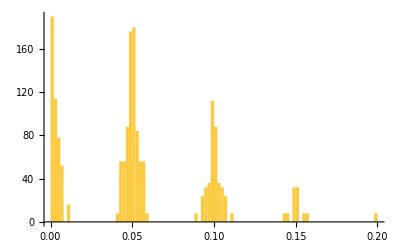

```mathematica
Histogram[nonzeroDiffs,100]
```

```mathematica
1/0.01
```

100.

```mathematica
1/0.05
```

20.

```mathematica
1/0.1
```

10.

```mathematica
bins=BinLists[nonzeroDiffs,{Min[nonzeroDiffs],Max[nonzeroDiffs],0.001}];
```

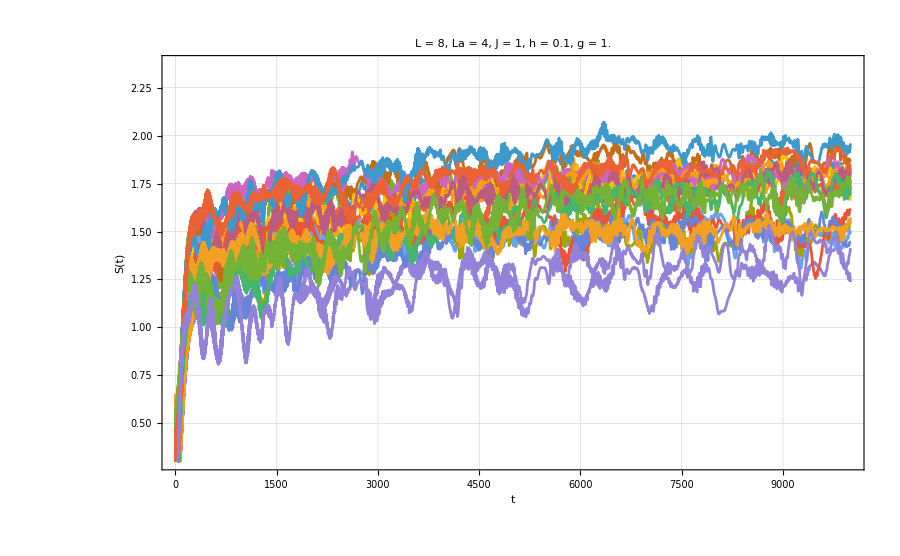

```mathematica
ListPlot[svntproductfull,PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}]
```